# MATRIX STRUCTURE

## For the left-handed chiral coupling matrices of the S_1 leptoquark.

## Initialization and constants

```mathematica
hbar=6.582119*10^-25; (*GeV*s*)
secPerYear=3600*24*365.25;
hbary=hbar/secPerYear;.08

(* CKM and PMNS matrices *)
V= {{0.97435,0.22501,0.00373},{0.22487,0.97349,0.04183},{0.00858,0.04111,0.99912}};
U={{0.82296,0.54843,0.14815},{0.27528,0.61286,0.74069},{0.49695,0.56888,0.65531}};

(* masses in GeV *)
mp=0.938272;
me=0.000511;
mmu=0.105658;
mpi0=0.134977;
mpiPlus=0.139570;
mK=0.493677;
meta = 0.54786;
mrho0=0.77503;
mrhoPlus=0.77511;
momega=0.78266;
mK0=0.49761;
mLQ=10000; (*10 TeV*)

(* Lattice QCD form factor *)
W0benchmark=0.1;
W0EpiL= 0.134;
W0EpiR=-0.131;
W0MupiL=0.119;
W0MupiR=-0.118;
W0NupiL=0.189;
W0NupiR=-0.186;
W0NuKR=-0.134;
W0NuKL=0.139;
W0EetaR=0.006;
W0EetaL=0.113;
W0MuetaR=0.011;
W0MuetaL=0.108;
AL = 1;


(* CM momentums: p=(1/(2mp))*Sqrt[(mp^2-mf1^2-mf2^2)^2-4*mf1^2*mf2^2] *)
pepi0=(1/(2*mp))*Sqrt[(mp^2-me^2-mpi0^2)^2-4*me^2*mpi0^2];
pmupi0=(1/(2*mp))*Sqrt[(mp^2-mmu^2-mpi0^2)^2-4*mmu^2*mpi0^2];
pnupiPlus=(1/(2*mp))*(mp^2-mpiPlus^2);
pnuK=(1/(2*mp))*(mp^2-mK^2);
peeta=(1/(2*mp))*Sqrt[(mp^2-me^2-meta^2)^2-4*me^2*meta^2];
pmueta=(1/(2*mp))*Sqrt[(mp^2-mmu^2-meta^2)^2-4*mmu^2*meta^2];
perho=(1/(2*mp))*Sqrt[(mp^2-me^2-mrho0^2)^2-4*me^2*mrho0^2];
pmurho=(1/(2*mp))*Sqrt[(mp^2-mmu^2-mrho0^2)^2-4*mmu^2*mrho0^2];
pnurho=(1/(2*mp))*(mp^2-mrhoPlus^2);
peomega=(1/(2*mp))*Sqrt[(mp^2-me^2-momega^2)^2-4*me^2*momega^2];
pmuomega=(1/(2*mp))*Sqrt[(mp^2-mmu^2-momega^2)^2-4*mmu^2*momega^2];
peK0=(1/(2*mp))*Sqrt[(mp^2-me^2-mK0^2)^2-4*me^2*mK0^2];
pmuK0=(1/(2*mp))*Sqrt[(mp^2-mmu^2-mK0^2)^2-4*mmu^2*mK0^2];

(* K prefactors assuming the leptoquark mass is inside this because we are taking it as a constant *)
KEpi0 = pepi0/(16*Pi*mp^2)*(AL^2 * W0EpiL^2)/mLQ^4*(mp^2+me^2-mpi0^2);
KMupi0= pmupi0/(16*Pi*mp^2)*(AL^2 * W0MupiL^2)/mLQ^4*(mp^2+mmu^2-mpi0^2);
KNupiPlus=pnupiPlus/(16*Pi*mp^2)*(AL^2 * W0NupiL^2)/mLQ^4*(mp^2-mpiPlus^2);
KNuK=pnuK/(16*Pi*mp^2)*(AL^2 * W0NuKL^2)/mLQ^4*(mp^2-mK^2);
KEeta=peeta/(16*Pi*mp^2)*(AL^2 * W0EetaL^2)/mLQ^4*(mp^2+me^2-meta^2);
KMueta=pmueta/(16*Pi*mp^2)*(AL^2 * W0MuetaL^2)/mLQ^4*(mp^2+mmu^2-meta^2);
KErho0= perho/(16*Pi*mp^2)*(AL^2 * W0benchmark^2)/mLQ^4*(mp^2+me^2-mrho0^2);
KMurho0=pmurho/(16*Pi*mp^2)*(AL^2 * W0benchmark^2)/mLQ^4*(mp^2+mmu^2-mrho0^2);
KNurhoPlus = pnurho/(16*Pi*mp^2)*(AL^2 * W0benchmark^2)/mLQ^4*(mp^2-mrhoPlus^2);
KEomega=peomega/(16*Pi*mp^2)*(AL^2 * W0benchmark^2)/mLQ^4*(mp^2+me^2-momega^2);
KMuomega=pmuomega/(16*Pi*mp^2)*(AL^2 * W0benchmark^2)/mLQ^4*(mp^2+mmu^2-momega^2);
```

.08

```mathematica
(* PDG experimental bounds (in years)*)
limEpi=2.4*10^34;
limMupi=1.6*10^34;
limNuPi=3.9*10^32;
limNuK=5.9*10^33;
limEeta=1.0*10^34;
limMueta=4.7*10^33;
limErho=7.2*10^32;
limMurho=5.7*10^32;
limNurho=1.62*10^32;
limEomega=1.6*10^33;
limMuomega=2.8*10^33;
```

## Monte Carlo scanner

### Core

```mathematica
ScanProtonDecay[nLimits_,numSamples_,maxexp_]:=Module[{results={},safetyFactors,minRobustness,bottleneckIdx,channelNames,bottleneck},
channelNames={"p->e+pi0","p->mu+pi0","p->nu+pi+","p->nu+K+"};

Do[
(*Assign random values*)
{y11,y12,y13,y21,y22,y23,y31,y32}=RandomInteger[{0,maxexp},8];
{z11,z12,z13,z22,z23}=RandomInteger[{0,maxexp},5];
eps=RandomReal[{10^-1,0.3}];

(*Reconstruct matrices*)
y1LL={{eps^y11,eps^y12,eps^y13},{eps^y21,eps^y22,eps^y23},{eps^y31,eps^y32,1}};
z1LL={{eps^z11,eps^z12,eps^z13},{eps^z12,eps^z22,eps^z23},{eps^z13,eps^z23,1}};

(*Effective matrices*)
yEff=V.y1LL;
zEff=V.z1LL;
hEff=y1LL.U;

(*Calculate lifetimes*)
tauEpi0=hbary/(KEpi0*Abs[zEff[[1,1]]*yEff[[1,1]]]^2);
tauMupi=hbary/(KMupi0*Abs[zEff[[1,1]]*yEff[[1,2]]]^2);
tauNuPi=hbary/(KNupiPlus*Abs[zEff[[1,1]]*(hEff[[1,1]]+hEff[[1,2]]+hEff[[1,3]])]^2);
tauNuK=hbary/(KNuK*Abs[zEff[[1,1]]*(hEff[[2,1]]+hEff[[2,2]]+hEff[[2,3]])]^2);

(*Check feasibility*)
isOk=Which[nLimits==1,tauEpi0>limEpi,nLimits==2,tauEpi0>limEpi&&tauMupi>limMupi,nLimits==3,tauEpi0>limEpi&&tauMupi>limMupi&&tauNuPi>limNuPi,nLimits==4,tauEpi0>limEpi&&tauMupi>limMupi&&tauNuPi>limNuPi&&tauNuK>limNuK];
If[isOk,
(*robustness of the solution*)
safetyFactors={tauEpi0/limEpi,tauMupi/limMupi,tauNuPi/limNuPi,tauNuK/limNuK};
minRobustness=Min[safetyFactors];
bottleneckIdx=Ordering[safetyFactors,1][[1]];
bottleneck=channelNames[[bottleneckIdx]];

(*results*)
AppendTo[results,{eps,y11,y12,y13,y21,y22,y23,y31,y32,z11,z12,z13,minRobustness,bottleneck}]],{numSamples}];
Return[results]];
```

### Ejecution

```mathematica
mysolutions=ScanProtonDecay[4,100000,23]; (* # of limits to fulfill, # of iterations, maximum exponent *)

(*Order results from less robust to most*)
sortedSolutions=SortBy[mysolutions,#[[13]]&];

(*Choose only the closest solutions to the limit*)
tightSolutions=Select[sortedSolutions,1<=#[[13]]<=50&];

Print["Number of solutions found: ",Length[mysolutions]];

(*Take first 5 of sortedSolutions*)
selectedRows=Join[Take[sortedSolutions,Min[5,Length[sortedSolutions]]]];

(*TABLE OF SOLUTIONS*)
TableForm[selectedRows,TableHeadings->{None,{"eps","y11","y12","y13","y21","y22","y23","y31","y32","z11","z12","z13","robustness factor","less robust channel"}}]
```

Number of solutions found: 145

eps | y11 | y12 | y13 | y21 | y22 | y23 | y31 | y32 | z11 | z12 | z13 | robustness factor | less robust channel
0.123625 | 18 | 15 | 19 | 17 | 5 | 13 | 12 | 1 | 23 | 21 | 21 | 1.0733 | p->mu+pi0
0.143687 | 20 | 10 | 7 | 18 | 15 | 21 | 11 | 11 | 22 | 22 | 17 | 1.08186 | p->nu+pi+
0.127866 | 21 | 13 | 4 | 14 | 4 | 23 | 18 | 4 | 23 | 21 | 21 | 1.08457 | p->nu+K+
0.105052 | 11 | 23 | 20 | 12 | 11 | 17 | 18 | 13 | 16 | 12 | 20 | 1.10965 | p->e+pi0
0.116967 | 18 | 14 | 21 | 15 | 23 | 17 | 12 | 20 | 19 | 10 | 12 | 1.15719 | p->mu+pi0

### Graphs

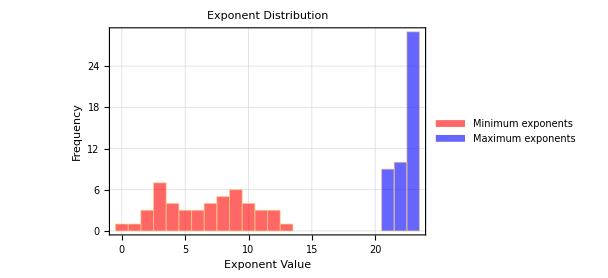

```mathematica
(*Prepare data for the tight solutions*)
tightMin=Min[#[[2;;12]]]&/@tightSolutions;
tightMax=Max[#[[2;;12]]]&/@tightSolutions;
maxRange=Max[tightMax];

(*Generate the main histogram*)
histogram=Histogram[{tightMin,tightMax},{-0.5,maxRange+0.5,1},PlotLabel->"Exponent Distribution",Frame->True,FrameLabel->{"Exponent Value","Frequency"},ChartLegends->{"Minimum exponents","Maximum exponents"},ChartStyle->{Directive[Red,Opacity[0.6]],Directive[Blue,Opacity[0.6]]},GridLines->Automatic,PlotRange->All,BaseStyle->{FontSize->14,FontFamily->"Helvetica"},LabelStyle->{FontSize->14,Bold},ImagePadding->{{45,15},{40,10}},ImageSize->450]
```

## Visualization: Interactive sliders

```mathematica
Manipulate[
(*Matrices Definition*)
y1LL={{eps^y11,eps^y12,eps^y13},{eps^y21,eps^y22,eps^y23},{eps^y31,eps^y32,1}};
z1LL={{eps^z11,eps^z12,eps^z13},{eps^z12,eps^z22,eps^z23},{eps^z13,eps^z23,1}};

(*Effective Matrices*)
yEff=V.y1LL;
zEff=V.z1LL;
hEff=y1LL.U;

(*Lifetime Calculations*)
tauEpi0=hbary/(KEpi0*Abs[zEff[[1,1]]*yEff[[1,1]]]^2);
tauMupi=hbary/(KMupi0*Abs[zEff[[1,1]]*yEff[[1,2]]]^2);
tauNuPi=hbary/(KNupiPlus*Abs[zEff[[1,1]]*(hEff[[1,1]]+hEff[[1,2]]+hEff[[1,3]])]^2);
tauNuK=hbary/(KNuK*Abs[zEff[[1,1]]*(hEff[[2,1]]+hEff[[2,2]]+hEff[[2,3]])]^2);
tauEeta=tauEpi0*KEpi0/KEeta;
tauMueta=tauMupi*KMupi0/KMueta;
tauErho=tauEpi0*KEpi0/KErho0;
tauMurho=tauMupi*KMupi0/KMurho0;
tauNurhoPlus=tauNuPi*KNupiPlus/KNurhoPlus;
tauEomega=tauEpi0*KEpi0/KEomega;
tauMuomega=tauMupi*KMupi0/KMuomega;

(*Visualization*)Column[{Style["Coupling Matrices (Flavor Basis)",Bold,16],Row[{Style["y1LL = ",14],MatrixForm[y1LL],Spacer[30],Style["z1LL = ",14],MatrixForm[z1LL]}],Spacer[20],Grid[{{Style["Results: Proton lifetime (years)",Bold,16]},{Grid[{{Style["Channel",Bold],Style["Theoretical Tau [years]",Bold],Style["PDG bound [years]",Bold],Style["Status",Bold]},{"p → e^+ π^0",ScientificForm[tauEpi0,3],ScientificForm[limEpi,3],If[tauEpi0>limEpi,Style["OK",Green,Bold],Style["EXCLUDED",Red,Bold]]},{"p → μ^+ π^0",ScientificForm[tauMupi,3],ScientificForm[limMupi,3],If[tauMupi>limMupi,Style["OK",Green,Bold],Style["EXCLUDED",Red,Bold]]},{"p → ν̄ π^+",ScientificForm[tauNuPi,3],ScientificForm[limNuPi,3],If[tauNuPi>limNuPi,Style["OK",Green,Bold],Style["EXCLUDED",Red,Bold]]},{"p → ν̄ K^+",ScientificForm[tauNuK,3],ScientificForm[limNuK,3],If[tauNuK>limNuK,Style["OK",Green,Bold],Style["EXCLUDED",Red,Bold]]},
{"p → e^+ η",ScientificForm[tauEeta,3],ScientificForm[limEeta,3],If[tauEeta>limEeta,Style["OK",Green,Bold],Style["EXCLUDED",Red,Bold]]},
{"p → μ^+ η",ScientificForm[tauMueta,3],ScientificForm[limMueta,3],If[tauMueta>limMueta,Style["OK",Green,Bold],Style["EXCLUDED",Red,Bold]]},
{"p → e^+ ρ^0",ScientificForm[tauErho,3],ScientificForm[limErho,3],If[tauErho>limErho,Style["OK",Green,Bold],Style["EXCLUDED",Red,Bold]]},
{"p → μ^+ ρ^0",ScientificForm[tauMurho,3],ScientificForm[limMurho,3],If[tauMurho>limMurho,Style["OK",Green,Bold],Style["EXCLUDED",Red,Bold]]},
{"p → ν̄ ρ^+",ScientificForm[tauNurhoPlus,3],ScientificForm[limNurho,3],If[tauNurhoPlus>limNurho,Style["OK",Green,Bold],Style["EXCLUDED",Red,Bold]]},
{"p → e^+ ω",ScientificForm[tauEomega,3],ScientificForm[limEomega,3],If[tauEomega>limEomega,Style["OK",Green,Bold],Style["EXCLUDED",Red,Bold]]},
{"p → μ^+ ω",ScientificForm[tauMuomega,3],ScientificForm[limMuomega,3],If[tauMuomega>limMuomega,Style["OK",Green,Bold],Style["EXCLUDED",Red,Bold]]}},
Frame->All,Background->{None,{LightGray,White}},Alignment->Left]}}]}],

(*Explicit Controls*)
Delimiter,
Style["Global Parameters",Bold],{{eps,0.1,"ϵ"},0.01,1,Appearance->"Labeled"},
Style["Exponents y1LL",Bold],
{{y11,5,"y11"},0,23,1,Appearance->"Labeled"},
{{y12,9,"y12"},0,23,1,Appearance->"Labeled"},
{{y13,9,"y13"},0,23,1,Appearance->"Labeled"},
{{y21,7,"y21"},0,23,1,Appearance->"Labeled"},
{{y22,21,"y22"},0,23,1,Appearance->"Labeled"},
{{y23,6,"y23"},0,23,1,Appearance->"Labeled"},
{{y31,13,"y31"},0,23,1,Appearance->"Labeled"},
{{y32,20,"y32"},0,23,1,Appearance->"Labeled"},
Style["Exponents z1LL",Bold],
{{z11,23,"z11"},0,23,1,Appearance->"Labeled"},
{{z12,23,"z12"},0,23,1,Appearance->"Labeled"},
{{z13,16,"z13"},0,23,1,Appearance->"Labeled"},
{{z22,1,"z22"},0,23,1,Appearance->"Labeled"},
{{z23,1,"z23"},0,23,1,Appearance->"Labeled"},
ControlPlacement->Left,TrackedSymbols:>All]
```